```mathematica
Needs["NumericalCalculus`"]
```

## Precompute joint element

```mathematica
precomputeElement[EL_,EJ_]:=Module[{t1,ϕ,ϕ1,int1,res},
t1=Table[
res=Table[
FindMinimum[EL/2 ϕ1^2-EJ Cos[ϕ-ϕ1], {ϕ1, s1}][[1]]
,{s1,-π,π,π/3.}];
{ϕ, Min[res]}
,{ϕ,-2π,2.π,π/1000.}];
Return[Interpolation[t1]];
];

getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+2π,4π]-2π]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);α=1;β=3;
(* Outer Elements *)
Ic1=Quantity[0.7*10^-6,"Ampere"];

(* Inner Elements *)
(*L2=Quantity[150*10^-12,"Henry"];*)
(*Ic2=Quantity[0.8*10^-6,"Ampere"];*)
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EL2=β EJ1
EL1=EL2/α
(*EL2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L2 1/Quantity["Joule"],"SI"]
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]*)
(*EJ2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic2 1/Quantity["Joule"],"SI"]*)
```

366.652

1099.96

1099.96

```mathematica
(1/(2 x2[0]/sf))*(10^-15/π)^2*10^9
```

0.175925

```mathematica
Quiet[
e1=precomputeElement[EL1,EJ1];
];
```

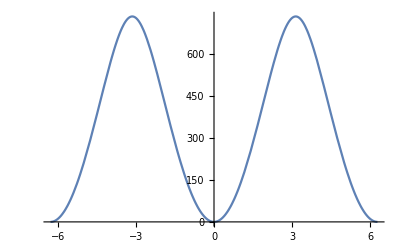

```mathematica
Plot[{getEnergy[e1,x]-getEnergy[e1,0],getEnergy[e2,x]-getEnergy[e2,0]},{x,-2π,2π}]
```

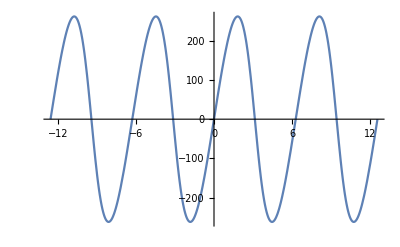

```mathematica
Plot[{D[getEnergy[e1,x],x]/.x->y,D[getEnergy[e2,x],x]/.x->y},{y,-4π,4π}]
```

## Construct the Hamiltonian_David

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[2*EJ1,ϕa-ϕf]+getEnergyLinInd[2*EJ1,ϕb-ϕf]+getEnergyLinInd[2*EJ1,ϕc-ϕf]+getEnergyLinInd[2*EJ1,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[2*EJ1,ϕa-ϕf]+getEnergyLinInd[2*EJ1,ϕb-ϕf]+getEnergyLinInd[2*EJ1,ϕc-ϕf]+getEnergyLinInd[2*EJ1,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],50];
Monitor[
t1=Table[
zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}];

zt1=({#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
zts=Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)];

Flatten[{ϕext,zts[[All,1]]}]
,{ϕext,0,4π,π/10}]
,ϕext];
```

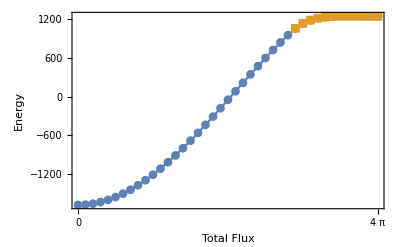

```mathematica
ListPlot[{t1[[All,{1,2}]],Select[t1,Length[#]≥3&][[All,{1,3}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{π Range[-8,8],Automatic}]
```

```mathematica
res={ϕa->0,ϕb->0,ϕc->0,ϕd->0,ϕf->0};
Monitor[
t2=Table[
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext]/.res;
{ϕext,(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[h0/.{a->1,ϕx->0.,ϕz->0,ϕw->0},{ϕy,2},0])/2,
(ND[h0/.{a->1,ϕx->0.,ϕy->0,ϕw->0},{ϕz,2},0])/2,
D[h0,ϕx,ϕy,ϕz]/.{a->1,ϕx->0,ϕy->0,ϕz->0,ϕw->0},
(*ND[ND[ND[h0/.{a->1,ϕw->0},ϕx,0],ϕy,0],ϕz,0],*)
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[ND[h0/.{a->1,ϕy->0,ϕw->0},{ϕx,2},0],{ϕz,2},0])/4,
(ND[ND[h0/.{a->1,ϕx->0,ϕw->0},{ϕy,2},0],{ϕz,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24,
(ND[h0/.{a->1,ϕx->0.,ϕz->0,ϕw->0},{ϕy,4},0])/24,
(ND[h0/.{a->1,ϕx->0.,ϕy->0,ϕw->0},{ϕz,4},0])/24}
,{ϕext,-4π*0,4π,π/10}];
,ϕext]
```

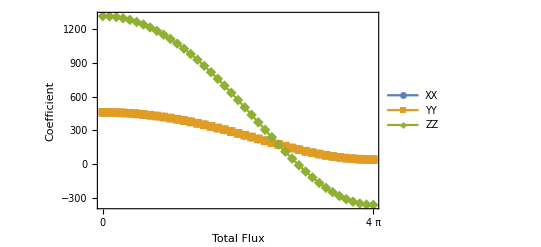

```mathematica
ListPlot[{t2[[All,{1,2}]],t2[[All,{1,3}]],t2[[All,{1,4}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"XX","YY","ZZ"}]]
```

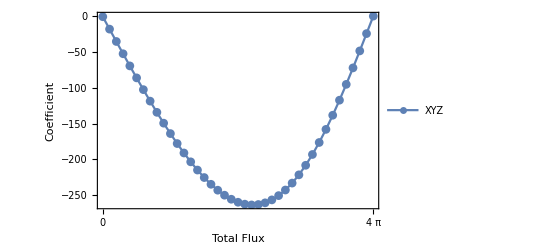

```mathematica
ListPlot[{t2[[All,{1,5}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"XYZ"}]]
```

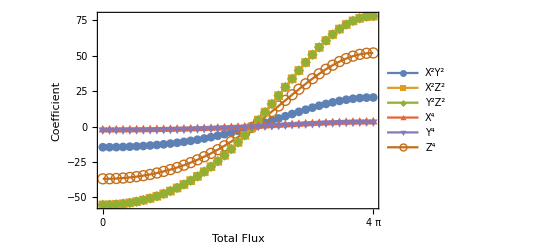

```mathematica
ListPlot[{t2[[All,{1,6}]],t2[[All,{1,7}]],t2[[All,{1,8}]],t2[[All,{1,9}]],t2[[All,{1,10}]],t2[[All,{1,11}]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{π Range[-8,8],Automatic}, PlotLegends->LineLegend[{"X^2Y^2","X^2Z^2","Y^2Z^2","X^4","Y^4","Z^4"}]]
```

## Construct the Hamiltonian_v2

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],100];
```

```mathematica
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/5}]
,ϕext];
```

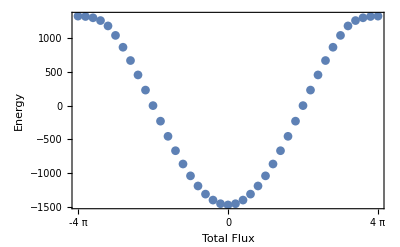

```mathematica
ListPlot[
{t1[[All,1,{1,2}]]},
 PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}}
]
```

#### Interpolation of all terms

```mathematica
Monitor[
t2=Table[
{ϕext,ϕa,ϕb,ϕc,ϕd}=t1[[i,1,{1,3,4,5,6}]];
ϕf=0;
(*xmin=sol[[3]]-sol[[5]];
ymin=sol[[2]]-sol[[4]];
zmin=(sol[[3]]+sol[[5]]-sol[[2]]-sol[[4]])/2;*)
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext];
{ϕext,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[h0/.{a->1,ϕx->0,ϕz->0,ϕw->0},{ϕy,2},0])/2,
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,6},0])/6!,
(ND[ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0],{ϕy,2},0])/48,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,8},0])/8!
}
,{i,Length[t1]}]
,t1[[i,1,1]]];
```

```mathematica
x2=Interpolation[t2[[All,{1,2}]]];
y2=Interpolation[t2[[All,{1,3}]]];
x2y2=Interpolation[t2[[All,{1,4}]]];
x4=Interpolation[t2[[All,{1,5}]]];
x6=Interpolation[t2[[All,{1,6}]]];
x4y2=Interpolation[t2[[All,{1,7}]]];
x8=Interpolation[t2[[All,{1,8}]]];
```

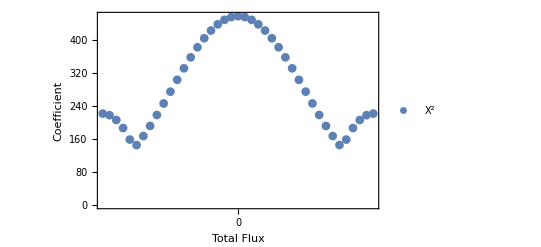

```mathematica
ListPlot[
{t2[[All,{1,2}]]}, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient"}, FrameTicks->{Automatic,{4π Range[0,16],None}}, PlotLegends->LineLegend[{"X^2","YY","ZZ"}],FrameStyle->Directive[Thick,14]
]
```

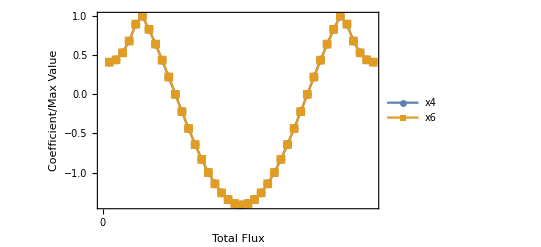

```mathematica
ListPlot[
{t2[[All,4]]/Max[t2[[All,4]]],t2[[All,5]]/Max[t2[[All,5]]]}, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Coefficient/Max Value"}, FrameTicks->{Automatic,{4π Range[0,16],None}}, PlotLegends->LineLegend[{"x4","x6","ZZ"}],FrameStyle->Directive[Thick,14],Joined->True
]
```

#### Participation ratio

```mathematica
Manipulate[
Plot[
{((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/.{la->La,lb->Lb},((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/.{la->La,lb->Lb},((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/.{la->La,lb->Lb}},
{x,0,8π},Frame->True, FrameLabel->{"Total Flux","Participation ratio"}, FrameTicks->{Automatic,{π Range[-8,16],None}},
FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"Px","Py","Pz"}]
]
,{La,0.0,4,0.01},{Lb,0.0,7,0.01}]
```

```mathematica
Manipulate[
Plot[
{(√(lb+(1/(2 y2[0]/sf))*(10^-15/π)^2*10^9))/(√(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))/.{la->La,lb->Lb}},
{x,0,8π},Frame->True, FrameLabel->{"Total Flux","Δf"}, FrameTicks->{Automatic,{π Range[-8,16],None}},
FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"Δf_x","Δf_y","Δf_z"}]
]
,{La,0.0,4,0.01},{Lb,0.0,7,0.01}]
```

#### Third order terms w/ & w/0 ps

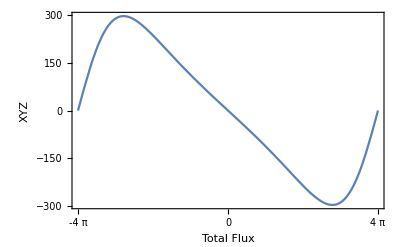

```mathematica
Plot[
xyz[x],{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","XYZ"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All
]
```

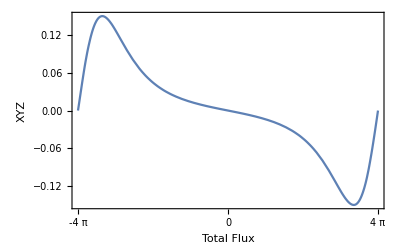

```mathematica
Plot[
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)xyz[x])/.{la->1.87,lb->1.84},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","XYZ"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All
]
```

#### Fourth order terms

Self-Kerr terms

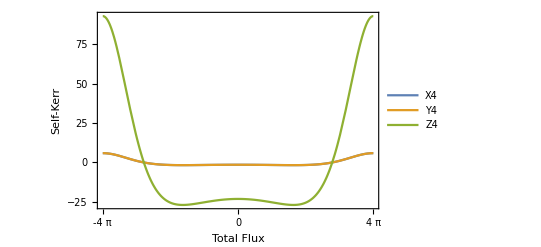

```mathematica
Plot[
{x4[x],y4[x],z4[x]},
{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X4","Y4","Z4"}]
]
```

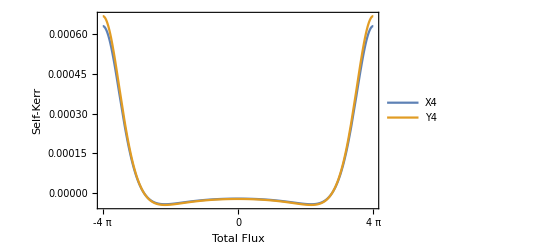

```mathematica
Plot[
{(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^4 x4[x]/.{la->1.87,lb->1.84},
(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^4 y4[x]/.{la->1.87,lb->1.84}
},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X4","Y4","Z4"}]
]
```

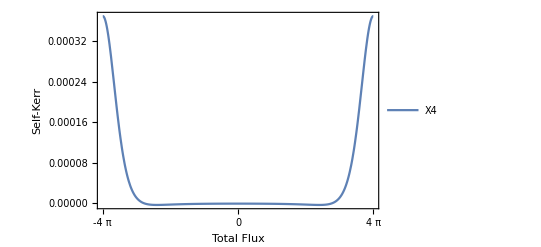

```mathematica
Plot[
(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^4 x4[x]/.{la->1.87,lb->1.84},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X4","Y4","Z4"}]
]
```

Cross-Kerr terms

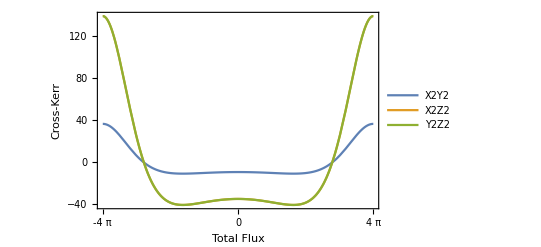

```mathematica
Plot[
{x2y2[x],x2z2[x],y2z2[x]},
{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Cross-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X2Y2","X2Z2","Y2Z2"}]
]
```

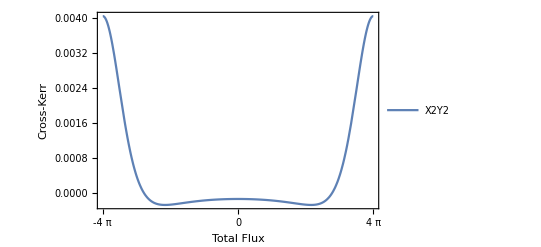

```mathematica
Plot[
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^2 x2y2[x]/.{la->1.87,lb->1.84},
{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Cross-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X2Y2","X2Z2","Y2Z2"}]
]
```

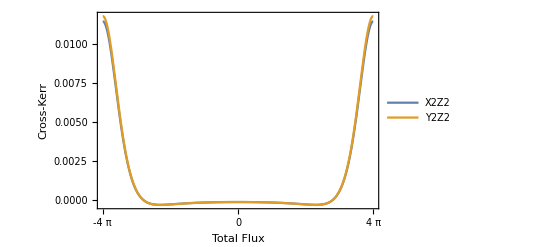

```mathematica
Plot[
{
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^2 x2z2[x]/.{la->1.87,lb->1.84},
(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^2 y2z2[x]/.{la->1.87,lb->1.84}
},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Cross-Kerr"}, FrameTicks->{Automatic,{π Range[-8,8],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X2Z2","Y2Z2"}]
]
```

## Phase Diagram_ideal

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergyJJ[EJ1,ϕa-ϕb-ϕx/4]+getEnergyJJ[EJ1,ϕb-ϕc-ϕx/4]+ getEnergyJJ[EJ1,ϕc-ϕd-ϕx/4]+getEnergyJJ[EJ1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],50];
sf=10^-9/(2 π 1*10^-34);
(* Outer Elements *)
L1=Quantity[√2 20*10^-12,"Henry"]; 
(* Inner Elements *)
L2=Quantity[20*10^-12,"Henry"];
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]
EL2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L2 1/Quantity["Joule"],"SI"]
```

6094.62

8619.1

```mathematica
βmin=1;βmax=5;βstep=0.1;
data=Table[i,{i,βmin,βmax,βstep}];
```

```mathematica
test=
Monitor[
Table[
(* Outer Elements *)
EJ1=EL2/data[[x]];
(*Quiet[
e1=precomputeElement[EL1,EJ1];
];*)
t1=Table[
zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}];
zt1=({ϕext,#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)]
,{ϕext,0,4π,π/10}];
data[[x]]=Table[Length[t1[[i]]],{i,Length[t1]}]
,{x,Length[data]}]
,data[[x]]];
```

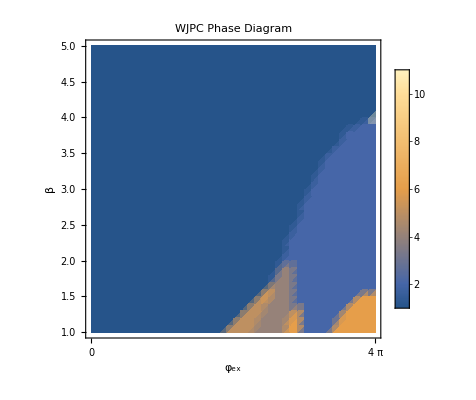

```mathematica
ListDensityPlot[
test,
PlotLegends->Automatic,DataRange->{{0,4π},{1,5}},FrameLabel->{"φ_ex","β"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLabel->Style["WJPC Phase Diagram",14],PlotRange->All
]
```

## Phase Diagram_real

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],50];
sf=10^-9/(2 π 1*10^-34);α=1;β=1;
(* Outer Elements *)
L1=Quantity[23*10^-12,"Henry"]; 
Ic1=Quantity[0.8*10^-6,"Ampere"];

(* Inner Elements *)
(*L2=Quantity[150*10^-12,"Henry"];*)
(*Ic2=Quantity[0.8*10^-6,"Ampere"];*)
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]
EL2=β EJ1
(*EL2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L2 1/Quantity["Joule"],"SI"]
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]*)
(*EJ2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic2 1/Quantity["Joule"],"SI"]*)
```

419.031

7494.87

419.031

```mathematica
Quiet[
e1=precomputeElement[EL1,EJ1];
];
```

```mathematica
βmin=2.5;βmax=2.5;βstep=0.1;
data=Table[i,{i,βmin,βmax,βstep}];
```

```mathematica
phasediag=
Monitor[
Table[

(* Inner Elements *)
EL2=EJ1 data[[x]];

t1=Table[
zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}];
zt1=({ϕext,#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)]
,{ϕext,0,4π,π/10}];
data[[x]]=Table[Length[t1[[i]]],{i,Length[t1]}]
,{x,Length[data]}]
,data[[x]]];
```

```mathematica
ListDensityPlot[
phasediag,
PlotLegends->Automatic,DataRange->{{0,4π},{1,5}},FrameLabel->{"φ_ex","β"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLabel->Style["WJPC Phase Diagram",14],PlotRange->All
]
```

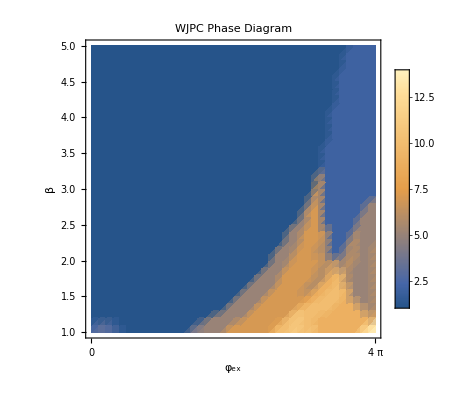

## Phase Diagram & 4th order Diagram

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],50];
sf=10^-9/(2 π 1*10^-34);
(* Outer Elements *)
L1=Quantity[23*10^-12,"Henry"]; 
Ic1=Quantity[0.8*10^-6,"Ampere"];

(* Inner Elements *)
(*L2=Quantity[150*10^-12,"Henry"];*)
(*Ic2=Quantity[0.8*10^-6,"Ampere"];*)
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]
```

419.031

7494.87

```mathematica
Quiet[
e1=precomputeElement[EL1,EJ1];
];
```

```mathematica
βmin=0.5;βmax=2.5;βstep=0.1;
data=Table[i,{i,βmin,βmax,βstep}]
```

{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5}

```mathematica
test=
Monitor[
Table[
(* Inner Elements *)
EL2=EJ1 data[[x]] ;

t1=Table[
zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}];
zt1=({ϕext,#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)]
,{ϕext,0,8π,π/10}];

res={ϕa->0,ϕb->0,ϕc->0,ϕd->0,ϕf->0};
allsol=t1[[All,1]][[All,{1,3,4,5,6}]];
t2=Table[
sol=allsol[[Position[allsol,ϕext1][[1,1]]]];
xmin=sol[[3]]-sol[[5]];
ymin=sol[[2]]-sol[[4]];
zmin=(sol[[3]]+sol[[5]]-sol[[2]]-sol[[4]])/2;
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext1]/.res;
{ϕext1,
(ND[h0/.{a->1,ϕy->ymin,ϕz->zmin,ϕw->0},{ϕx,2},xmin])/2
}
,{ϕext1,0,8π,π/10}];

(*x4=Interpolation[t2];*)

(*data[[x]]={(x/.FindRoot[x4[x]==0,{x,10}])/π,t2[[All,2]],Table[Length[t1[[i]]],{i,Length[t1]}]}*)
data[[x]]={t2[[All,2]],Table[Length[t1[[i]]],{i,Length[t1]}]}
,{x,Length[data]}]
,data[[x]]];
```

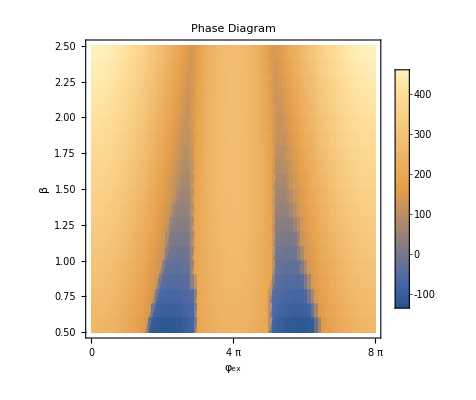

```mathematica
ListDensityPlot[
test[[All,1]],
PlotLegends->Automatic,DataRange->{{0,8π},{0.5,2.5}},FrameLabel->{"φ_ex","β"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLabel->Style["Phase Diagram",14],PlotRange->All
]
```

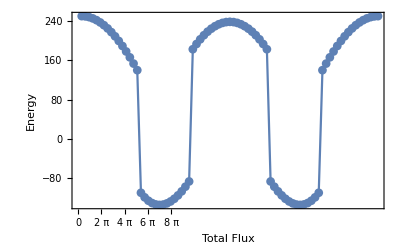

```mathematica
ListPlot[{test[[1,1]]}, Joined->True, PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{π Range[0,8],Automatic}]
```

## Find 4th order crossing points

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
ip=Table[RandomReal[{0,2π},4],100];
```

```mathematica
β=5;
sf=10^-9/(2 π 1*10^-34);
(* Outer Elements *)
L1=Quantity[√2 40*10^-12,"Henry"]; 
(*Ic1=Quantity[1.5*10^-6,"Ampere"];*)

(* Inner Elements *)
(*L2=Quantity[40*10^-12,"Henry"];*)
(*Ic2=Quantity[1.4*2.4*10^-6,"Ampere"];*)

EL1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L1 1/Quantity["Joule"],"SI"]
```

3047.31

```mathematica
αmin=0.4;αmax=1.4;αstep=0.1;
data=Table[i,{i,αmin,αmax,αstep}];
```

```mathematica
crosspoints=
Monitor[
Table[
(* Inner Elements *)
EL2=data[[x]] EL1;
EJ1=EL2/β;

Quiet[
e1=precomputeElement[EL1,EJ1];
];

t1=Table[
zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[i,1]]},{ϕb,ip[[i,2]]},{ϕc,ip[[i,3]]},{ϕd,ip[[i,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{i,Length[ip]}];
zt1=({ϕext,#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)]
,{ϕext,0,4π,π/10}];

res={ϕa->0,ϕb->0,ϕc->0,ϕd->0,ϕf->0};
allsol=t1[[All,1]][[All,{1,3,4,5,6}]];
t2=Table[
sol=allsol[[Position[allsol,ϕext1][[1,1]]]];
xmin=sol[[3]]-sol[[5]];
ymin=sol[[2]]-sol[[4]];
zmin=(sol[[3]]+sol[[5]]-sol[[2]]-sol[[4]])/2;
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext1]/.res;
{ϕext1,
(ND[ND[h0/.{a->1,ϕz->zmin,ϕw->0},{ϕx,2},xmin],{ϕy,2},ymin])/4
}
,{ϕext1,0,4π,π/10}];

x4=Interpolation[t2];
data[[x]]=(x/.FindRoot[x4[x]==0,{x,10}])/π
,{x,Length[data]}]
,data[[x]]]
```

{2.39645,2.48857,2.57673,2.6607,2.7404,2.81586,2.88718,2.95452,3.01812,3.07817,3.13487}

## α and β sweep

```mathematica
H[ϕa_,ϕb_,ϕc_,ϕd_,ϕf_,ϕx_]:=
(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
Hn[ϕa_?NumericQ,ϕb_?NumericQ,ϕc_?NumericQ,ϕd_?NumericQ,ϕf_?NumericQ,ϕx_?NumericQ]:=(getEnergy[e1,ϕa-ϕb-ϕx/4]+getEnergy[e1,ϕb-ϕc-ϕx/4]+ getEnergy[e1,ϕc-ϕd-ϕx/4]+getEnergy[e1,ϕd-ϕa-ϕx/4])+(getEnergyLinInd[EL2,ϕa-ϕf]+getEnergyLinInd[EL2,ϕb-ϕf]+getEnergyLinInd[EL2,ϕc-ϕf]+getEnergyLinInd[EL2,ϕd-ϕf]);
```

```mathematica
sf=10^-9/(2 π 1*10^-34);
ip=Table[RandomReal[{0,2π},4],100];
res1={ϕa->0,ϕb->0,ϕc->0,ϕd->0,ϕf->0};
L2=Quantity[20*10^-12,"Henry"];
EL2=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))^2 1./L2 1/Quantity["Joule"],"SI"]
```

8619.1

```mathematica
Monitor[
allres=
Table[
EL1=EL2/α;
EJ1=EL2/β;
Quiet[
e1=precomputeElement[EL1,EJ1];
];
t2=Table[

zt=Table[
res=Quiet[FindMinimum[Hn[ϕa,ϕb,ϕc,ϕd,0,ϕext],{ϕa,ip[[k,1]]},{ϕb,ip[[k,2]]},{ϕc,ip[[k,3]]},{ϕd,ip[[k,4]]}]];
{res[[1]],ϕa,ϕb,ϕc,ϕd}/.res[[2]]
,{k,Length[ip]}];
zt1=({ϕext,#[[1]],Mod[#[[2]]+0.1,2π]-0.1,Mod[#[[3]]+0.1,2π]-0.1,Mod[#[[4]]+0.1,2π]-0.1,Mod[#[[5]]+0.1,2π]-0.1}&/@Sort[zt])//Chop;
sol=Union[zt1,SameTest->(Total[Abs[#1-#2]]<10^-3&)][[1]];
xmin=sol[[4]]-sol[[6]];
ymin=sol[[3]]-sol[[5]];
zmin=(sol[[4]]+sol[[6]]-sol[[3]]-sol[[5]])/2;
h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕa,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕb,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕc,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕd,-a ϕw+ϕf, ϕext]/.res1;
{α,β,ϕext,
(ND[h0/.{a->1,ϕy->ymin,ϕz->zmin,ϕw->0},{ϕx,2},xmin])/2,
(ND[h0/.{a->1,ϕx->xmin,ϕz->zmin,ϕw->0},{ϕy,2},ymin])/2,
(ND[h0/.{a->1,ϕx->xmin,ϕy->ymin,ϕw->0},{ϕz,2},zmin])/2,
D[h0,ϕx,ϕy,ϕz]/.{a->1,ϕx->xmin,ϕy->ymin,ϕz->zmin,ϕw->0},
(ND[ND[h0/.{a->1,ϕz->zmin,ϕw->0},{ϕx,2},xmin],{ϕy,2},ymin])/4,
(ND[ND[h0/.{a->1,ϕy->ymin,ϕw->0},{ϕx,2},xmin],{ϕz,2},zmin])/4,
(ND[ND[h0/.{a->1,ϕx->xmin,ϕw->0},{ϕy,2},ymin],{ϕz,2},zmin])/4,
(ND[h0/.{a->1,ϕy->ymin,ϕz->zmin,ϕw->0},{ϕx,4},xmin])/24,
(ND[h0/.{a->1,ϕx->xmin,ϕz->zmin,ϕw->0},{ϕy,4},ymin])/24,
(ND[h0/.{a->1,ϕx->xmin,ϕy->ymin,ϕw->0},{ϕz,4},zmin])/24,
(ND[ND[h0/.{a->1,ϕy->ymin,ϕw->0},{ϕx,2},xmin],{ϕz,1},zmin])/2
}
,{ϕext,0,4π,π/10}];
{α,β,t2}
,{α,1.0,1.4,0.1},{β,1.0,5.0,0.2}]
,{α,β,ϕext,ProgressIndicator[(α/1.4+β/5.0+ϕext/(4π))/(5*41*41)]}];
```

```mathematica
Manipulate[
s1=ListPlot[
allres[[α,β,3]][[All,{3,4}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"X^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Blue
];
s2=ListPlot[
allres[[α,β,3]][[All,{3,5}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"Y^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Blue
];
s3=ListPlot[
allres[[α,β,3]][[All,{3,6}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"Z^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Blue
];
s4=ListPlot[
allres[[α,β,3]][[All,{3,7}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"XYZ : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Red
];
s5=ListPlot[
allres[[α,β,3]][[All,{3,14}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"X^2Z : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotRange->{-1500,1500},PlotStyle->Red
];
s6=ListPlot[
allres[[α,β,3]][[All,{3,11}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"X^4 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Purple
];
s7=ListPlot[
allres[[α,β,3]][[All,{3,12}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"Y^4 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Purple
];
s8=ListPlot[
allres[[α,β,3]][[All,{3,13}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"Z^4 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Purple
];
s9=ListPlot[
allres[[α,β,3]][[All,{3,8}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"X^2Y^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Black
];
s10=ListPlot[
allres[[α,β,3]][[All,{3,9}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"X^2Z^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Black
];
s11=ListPlot[
allres[[α,β,3]][[All,{3,10}]],
Frame->True,FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,{π Range[0,4π],None}},FrameLabel->{"ϕext","Coefficient / EJ"},
PlotLabel->"Z^2Y^2 : α = "<>ToString[allres[[α,1,1]]]<>" β = "<>ToString[allres[[1,β,2]]],Joined->True,PlotMarkers->Automatic,ImageSize->Medium,PlotStyle->Black
];
Grid[s1,s2,s3,s4,s5,s6,s7,s8,s9,s10,s11]
,{α,1,5,1},{β,1,21,1}]
```

## Comparing with Flux Sweep

#### Flux Sweep_signal

```mathematica
data=Import["E:\\BoxSync\\TZC\\Theory Projects\\WJPC\\20180209 WJPC21 6th order terms\\WJPC0021_idler_res_freq.csv","CSV"];
```

```mathematica
(*fluxsweep=Reverse/@data;*)
```

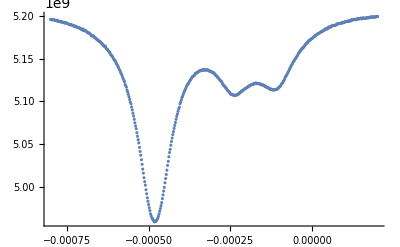

```mathematica
ListPlot[data]
```

```mathematica
flux=Table[i,{i,0,8π,8π/Length[data]}];
```

```mathematica
haha=Table[{flux[[i]],data[[i,2]]/Max[data[[All,2]]]},{i,Length[data]}];
```

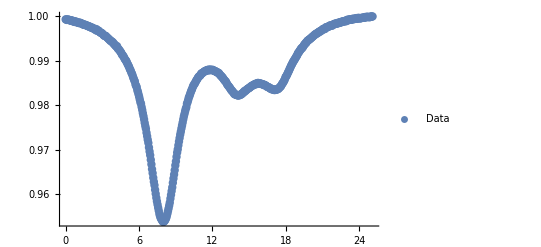

```mathematica
s1=ListPlot[haha,PlotLegends->{"Data"},PlotStyle->PointSize[0.015]]
```

```mathematica
Manipulate[
s2=Plot[
(√(lb+(1/(2 x2[0]/sf))*(10^-15/π)^2*10^9))/(√(lb+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))/.lb->i,{x,-4π,4π},Frame->True, FrameLabel->{"Total Flux","f/f_max"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotLegends->LineLegend[{"Y^2"}],PlotStyle->Red,ImageSize->Medium
];
s3=Plot[
{((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/.{lb->i}},
{x,-4π,4π},Frame->True, FrameLabel->{"Total Flux","Participation ratio"}, FrameTicks->{Automatic,{4π Range[0,16],None}},
FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"Py"}],ImageSize->Medium
];
Grid[Show[s2],s3]
,{i,1,10,0.1}]
```

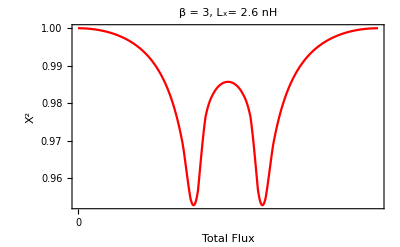

```mathematica
s4=Plot[
(√(lb+(1/(2 x2[0]/sf))*(10^-15/π)^2*10^9))/(√(lb+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))/.{lb->2.6},{x,0,8π},
Frame->True, FrameLabel->{"Total Flux","X^2"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotStyle->Red,PlotLabel->"β = 3, L_x= 2.6 nH"
]
```

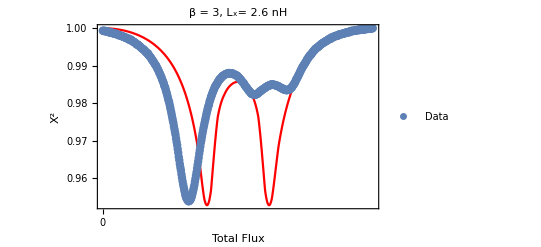

```mathematica
Show[s4,s1]
```

#### Check Z..characteristic impedance

```mathematica
Max[data[[All,2]]]
```

7.74413×10^9

```mathematica
Solve[2π 7.74413*10^9==1/(√(x (1.8*10^-9+0.315789*10^-9)))]
```

{{x→1.99629×10^-13}}

Characteristic impedance, Z,  is calculated at the below

```mathematica
√((1.87*10^-9)/(1.99629*10^-13))
```

96.7852

#### Plotting mixing term and 4th order terms

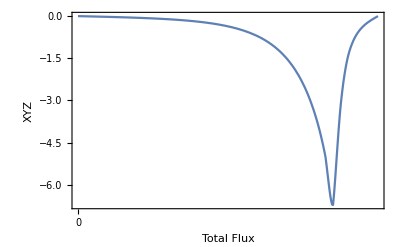

```mathematica
Plot[
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/4)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)xyz[x])/.{la->1.87,lb->1.87},{x,0,4π},
Frame->True, FrameLabel->{"Total Flux","XYZ"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotRange->All
]
```

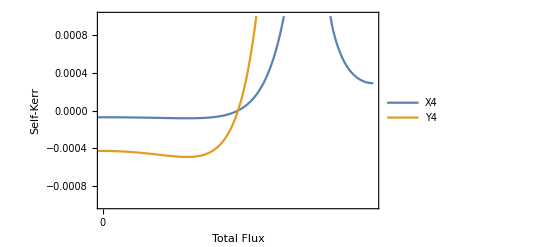

```mathematica
Plot[
{(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^4 x4[x]/.{la->2.5,lb->2.5},
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^2 x2y2[x]/.{la->2.5,lb->2.5}
},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotLegends->LineLegend[{"X4","Y4","Z4"}],PlotRange->{{0,4π},{-0.001,0.001}}
]
```

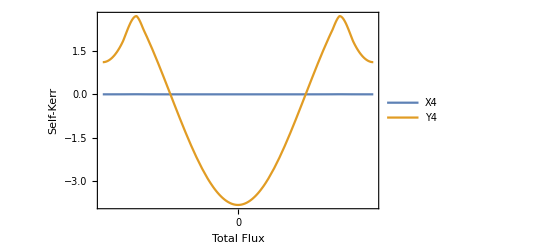

```mathematica
Plot[
{(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^4 x4[x]/.{la->2.5,lb->2.5},
x4[x]/.{la->2.5,lb->2.5}
},{x,-4π,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotLegends->LineLegend[{"X4","Y4","Z4"}],PlotRange->All
]
```

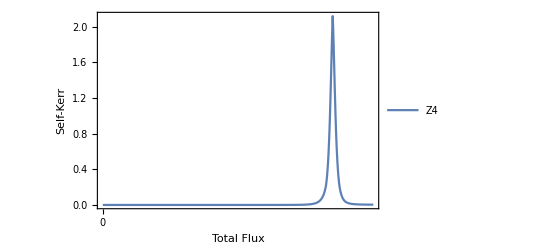

```mathematica
Plot[
(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^4 x4[x]/.{la->1.87,lb->1.8},{x,0,4π},
Frame->True, FrameLabel->{"Total Flux","Self-Kerr"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"Z4"}]
]
```

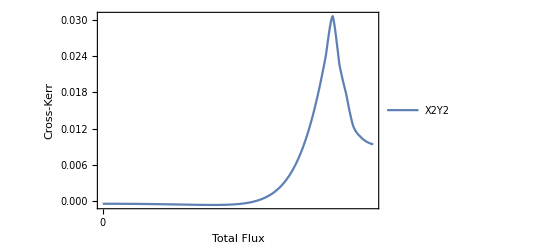

```mathematica
Plot[
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^2 x2y2[x]/.{la->1.87,lb->1.8},
{x,0,4π},
Frame->True, FrameLabel->{"Total Flux","Cross-Kerr"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X2Y2","X2Z2","Y2Z2"}]
]
```

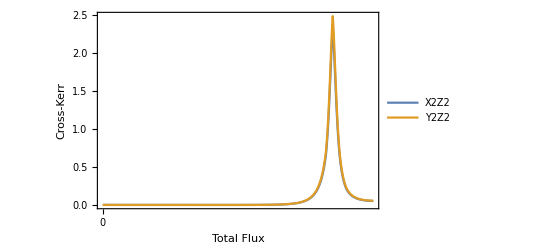

```mathematica
Plot[
{
(((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^2 x2z2[x]/.{la->1.87,lb->1.8},
(((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9))^2(((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9))^2 y2z2[x]/.{la->1.87,lb->1.8}
},{x,0,4π},
Frame->True, FrameLabel->{"Total Flux","Cross-Kerr"}, FrameTicks->{Automatic,{4π Range[0,16],None}},FrameStyle->Directive[Thick,14],PlotRange->All,PlotLegends->LineLegend[{"X2Z2","Y2Z2"}]
]
```

## Prediction of Pump Power to Obtain 20 dB Gain at Each External Flux

#### 1. Define functions

Starting from here, we solve max peak and ϵ numerically.

```mathematica
gain[κa_,κb_,g_,phoc_,m_,n_,a_,b_,Δ_,ϵ_]:=(16 g^4 phoc^4+8 g^2 phoc^2 (-4 (m phoc^2+Δ) (b+n phoc^2-Δ+ϵ)+κa κb)+4 a^2 (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+(4 (m phoc^2+Δ)^2+κa^2) (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+8 a (4 (b+n phoc^2-Δ+ϵ) (-g^2 phoc^2+(m phoc^2+Δ) (b+n phoc^2-Δ+ϵ))+(m phoc^2+Δ) κb^2))/(16 g^4 phoc^4+8 g^2 phoc^2 (-4 (m phoc^2+Δ) (b+n phoc^2-Δ+ϵ)-κa κb)+4 a^2 (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+(4 (m phoc^2+Δ)^2+κa^2) (4 (b+n phoc^2-Δ+ϵ)^2+κb^2)+8 a (4 (b+n phoc^2-Δ+ϵ) (-g^2 phoc^2+(m phoc^2+Δ) (b+n phoc^2-Δ+ϵ))+(m phoc^2+Δ) κb^2)); (* this is the function of gain from Rgain2 *)
computeΔmax[κa_,κb_,g_,phoc_,m_,n_,a_,b_,ϵ_]:=1/2 (-a+b-m phoc^2+n phoc^2+ϵ)+(-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)/(12 2^(2/3) (-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2+√(4 (-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)^3+(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2)^2))^(1/3))-1/(24 2^(1/3))(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2+√(4 (-48 a^2-96 a b-48 b^2+192 g^2 phoc^2-96 a m phoc^2-96 b m phoc^2-96 a n phoc^2-96 b n phoc^2-48 m^2 phoc^4-96 m n phoc^4-48 n^2 phoc^4-96 a ϵ-96 b ϵ-96 m phoc^2 ϵ-96 n phoc^2 ϵ-48 ϵ^2+24 κa^2+24 κb^2)^3+(-864 a κa^2-864 b κa^2-864 m phoc^2 κa^2-864 n phoc^2 κa^2-864 ϵ κa^2+864 a κb^2+864 b κb^2+864 m phoc^2 κb^2+864 n phoc^2 κb^2+864 ϵ κb^2)^2))^(1/3);  (* this is the function for max peak *) 
maxGain[κa_,κb_,g_,phoc_,m_,n_,a_,b_,ϵ_]:=Module[{Δmax}, 
Δmax=computeΔmax[κa,κb,g,phoc,m,n,a,b,ϵ];
Return[gain[κa,κb,g,phoc,m,n,a,b,Δmax,ϵ]];
];  (* This function return the value of gain when Δ=Δmax *)
Gvsϵ[κa_,κb_,g_,GG_,m_,n_,a_,b_,ϵ_,phoc0_]:=Module[{phoc,res},
res=FindRoot[maxGain[κa,κb,g,phoc,m,n,a,b,ϵ]==GG,{phoc,phoc0}];
Return[phoc/.res];
];(* This function return phoc with given pump power *)
```

#### 2. Give parameters

```mathematica
paarray=Table[((1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/(la+(1/(2 x2[x]/sf))*(10^-15/π)^2*10^9)/.{la->1.87,lb->1.8},{x,0,4π,π/10}];
pbarray=Table[((1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/(lb+(1/(2 y2[x]/sf))*(10^-15/π)^2*10^9)/.{la->1.87,lb->1.8},{x,0,4π,π/10}];
pcarray=Table[((1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/(((la+lb)/2)+(1/(2 z2[x]/sf))*(10^-15/π)^2*10^9)/.{la->1.87,lb->1.8},{x,0,4π,π/10}];
```

```mathematica
(* Give parameters *)
κa=2 π 0.02;κb=2 π 0.02;GG=100;
```

```mathematica
allsol=
Table[

code=t2[[i]];
condition={za->61.0,zb->77.0,zc->50.0,pa->paarray[[i]],pb->pbarray[[i]],pc->pcarray[[i]],ℏ->1.05457*10^-34,Subscript[φ, 0]->(2.0678*10^-15)/(2 π)};
g=2π code[[5]](pa pb pc ℏ √(za zb zc ℏ))/(2 √2 Subscript[φ, 0]^3)/.condition;αα=-2π code[[9]](ℏ^2 pa^4 za^2)/(4 Subscript[φ, 0]^4)/.condition;ββ=-2π code[[10]](ℏ^2 pb^4 zb^2)/(4 Subscript[φ, 0]^4)/.condition;γγ=-2π code[[11]](ℏ^2 pc^4 zc^2)/(4 Subscript[φ, 0]^4)/.condition;δδ=-2π code[[6]](ℏ^2 pa^2 pb^2 za zb)/(4 Subscript[φ, 0]^4)/.condition;λλ=-2π code[[7]](ℏ^2 pa^2 pc^2 za zc)/(4 Subscript[φ, 0]^4)/.condition;ϵϵ=-2π code[[8]](ℏ^2 pb^2 pc^2 zb zc)/(4 Subscript[φ, 0]^4)/.condition;
a=(12αα+2δδ+2λλ);
b=(12ββ+2δδ+2ϵϵ);m=4λλ;n=4λλ;l=4δδ;

t1=
Table[
Quiet[Gvsϵ[κa,κb,g,GG,m,n,a,b,0,phoc0]]
,{phoc0,0.0001,2,0.1}];

Flatten[{(i-1)π/10,Union[Abs[t1], SameTest->(Abs[#1-#2]<10^-4&)]}]

,{i,Length[t2]}];
```

```mathematica
tt=Table[{allsol[[i,1]],70+10*Log10[1/0.001 allsol[[i,2]]^2*1/0.0005*1.05457*^-34*2 π 12.544*10^9*2π 0.02*10^9]},{i,1,Length[t2]}];
```

```mathematica
root=x/.FindRoot[x4[x]==0,{x,3π}]
```

6.39498

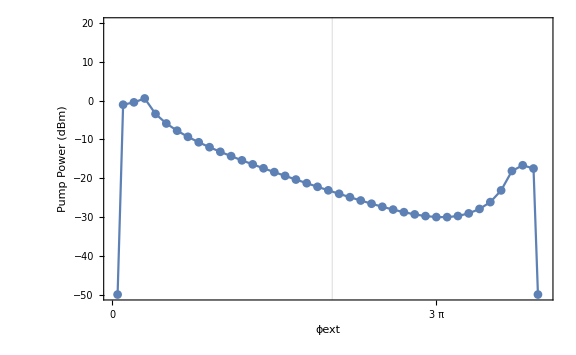

```mathematica
ListPlot[
tt, 
Frame->True,ImageSize->Large, FrameLabel->{"ϕext","Pump Power (dBm)"}, FrameStyle->Directive[Thick,14],Joined->True, PlotMarkers->Automatic,FrameTicks->{Automatic,{π Range[0,16],None}},PlotRange->{-50,20},
GridLines->{{{root,{Red,Thick}}},None}
]
```